## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
thesisPath="Thesis\\Figures\\";
```

```mathematica
<<MaTeX`
TeX=MaTeX[#,"Preamble"->{
"\\usepackage{mathpazo}",
"\\usepackage[mathscr]{euscript}"
},FontSize->14]&;
TeXS=MaTeX[#,"Preamble"->{
"\\usepackage{mathpazo}",
"\\usepackage[mathscr]{euscript}"
},FontSize->10]&;
```

```mathematica
<<"Definitions/IO.wl"
<<"Definitions/Teukolsky.wl"
<<"Definitions/SWSH.wl"
```

```mathematica
plotDirs={
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"TeXGyrePagella",FontSize->14},
FrameTicksStyle-> Directive[Black],
Axes->{True,False},
ImageSize->400};
Clear[TicksHidden,TicksNormal,TicksParse];
TicksNormal[t_]:={If[StringQ[#],ToExpression[#,TeXForm],#],
If[!NumericQ[#],
If[MatchQ[#,Rational[α_,β_]γ_.],
TeX@First@StringCases[ToString@TeXForm[#],"\\frac{"~~x__~~"}{"~~y__~~"}":>StringTrim[x]<>"/"<>StringTrim[y]],
TeX@#],
If[NumberQ[#],
If[IntegerPart[#]==#,
TeX@IntegerPart@#,
TeX@#],
If[MatchQ[#,Rational[α_,β_]γ_.],
TeX@First@StringCases[ToString@TeXForm[#],"\\frac{"~~x__~~"}{"~~y__~~"}":>StringTrim[x]<>"/"<>StringTrim[y]],
TeX@#]
]],{0.015,0}}&/@Chop@t
TicksHidden[t_]:={If[StringQ[#],ToExpression[#,TeXForm],#],"",{0.015,0}}&/@t
TicksParse[t_]:={TicksNormal@t,TicksHidden@t};
```

## More data

```mathematica
(*Export[GetSWSHEigenFile[1,#1,#2,"Leaver"],ParallelTable[{c,EigenLeaver[-1,#1,#2,c]},{c,0,10,0.01}]]&@@@Flatten[Table[{l,m},{l,1,5},{m,-l,l}],1]*)
```

```mathematica
(*Export[GetSWSHEigenFile[1,#1,#2,"Spectral"],ParallelTable[{c,SpinWeightedSpheroidalHarmonicEigenvalue[-1,#1,#2,c]},{c,0,10,0.01}]]&@@@Flatten[Table[{l,m},{l,1,5},{m,-l,l}],1]*)
```

## Eigenvalue plots

```mathematica
leaverFiles=First/@GroupBy[Cases[({#}~Join~StringSplit[#,{"\\","_","."}]&)/@GetSWSHEigenFile[],{___,"Leaver",___}],ToExpression@Take[#,{7,8}]&->First];
spectralFiles=First/@GroupBy[Cases[({#}~Join~StringSplit[#,{"\\","_","."}]&)/@GetSWSHEigenFile[],{___,"Spectral",___}],ToExpression@Take[#,{7,8}]&->First];
```

### Discontinuities plot

```mathematica
ticksEV={TicksParse@{-6,-2,2,6,12,20},TicksParse@Range[0,3,0.5]};
```

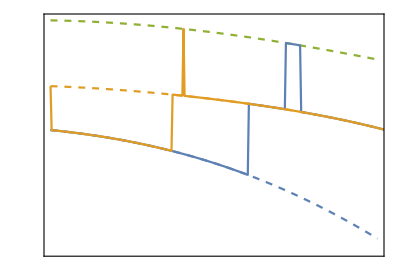
-Graphics--Graphics-

```mathematica
plot1={Plot[Interpolation[ImportCSV[spectralFiles[{#,1}]]][c]&/@{1,2,3}//Evaluate,{c,0,3.0},PlotStyle->Dashed,Frame->True],
ListPlot[ImportCSV[leaverFiles[{#,1}]]&/@{1,2},Joined->True,Frame->True,
PlotLegends->LineLegend[ColorData[97,#]&/@Range[3],TeX[{"1","2","3"}],LegendLabel->TeX["\\ell"],LegendFunction->Panel]]
}//Labeled[Show[#,
PlotRange->{{0,3},Automatic},plotDirs,
PlotRangePadding->{0,{0.5,1.5}},
FrameLabel->{TeX@"c",None},
FrameTicks->ticksEV,
AspectRatio->0.7
],TeX["{}_{\\pm 1}\\mathscr{E}_{\ell 1}\\hspace{2cm}"],Top,Spacings->{0,-0.6}]&
Export[thesisPath<>"discontinuitiesEV.pdf",plot1];
```

### l=1 plots

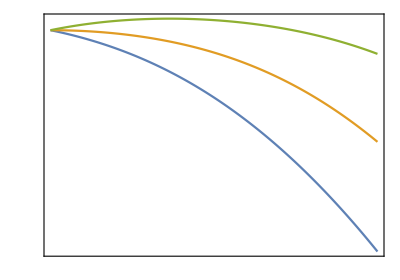
-Graphics--Graphics-

```mathematica
list2={1,0,-1};
plot2=ListPlot[
Cases[ImportCSV[spectralFiles[{1,#}]],{c_,ev_}/;0≤c≤3]&/@list2,
Joined->True,Frame->True,
PlotLegends->Placed[LineLegend[ColorData[97,#]&/@Range@Length@list2,TeX[list2],
LegendFunction->Panel,LegendLayout->"Column",LegendLabel->TeX["m"]],{0.12,0.28}]
]//Labeled[Show[#,
PlotRange->{{0,3},Automatic},plotDirs,
PlotRangePadding->{0,{0.5,1.0}},
FrameLabel->{TeX@"c",None},
FrameTicks->ticksEV,
AspectRatio->0.7
],TeX["\\quad {}_{\\pm 1}\\mathscr{E}_{1 m}"],Top,Spacings->{Automatic,-0.6}]&
Export[thesisPath<>"plotEV1.pdf",plot2];
```

```mathematica
swsh1=(#->ParallelTable[{θ,SpinWeightedSpheroidalHarmonicS[-1,1,#,0.4,θ,0]},{θ,0,Pi,Pi/200.}]&)/@{-1,0,1}//Association;
```

```mathematica
ticksSWSH1={TicksParse@Range[-0.5,0.0,0.1],TicksParse@Range[0,π,π/4]};
```

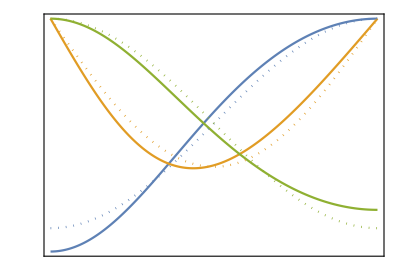
-Graphics--Graphics-

```mathematica
plot4={
ListPlot[swsh1/@{1,0,-1},Joined->True],
Plot[SpinWeightedSphericalHarmonicY[-1,1,#,θ,0]&/@{1,0,-1}//Evaluate,{θ,0,π},PlotStyle->Dotted]
}//Labeled[Show[#,plotDirs,
PlotRangePadding->{0,0.02},
FrameLabel->{TeX@"\\theta",None},
FrameTicks->ticksSWSH1,
AspectRatio->0.7
],TeX["\\qquad{}_{-1}S_{1 m}(c=0.4 \\,; \\,\\theta, 0)"],Top,Spacings->{0,-0.6}]&
Export[thesisPath<>"plotSWSH1.pdf",plot4];
```

### l=2 plots

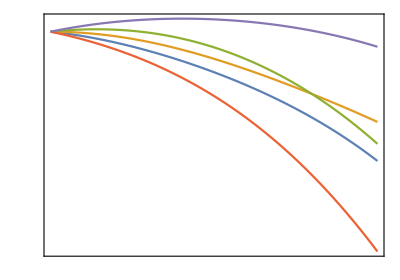
-Graphics--Graphics-

```mathematica
list3=list2~Join~{2,-2};
plot3=ListPlot[
Cases[ImportCSV[spectralFiles[{2,#}]],{c_,ev_}/;0≤c≤3]&/@list3,
Joined->True,Frame->True,
PlotLegends->Placed[LineLegend[ColorData[97,#]&/@Range@Length@list3,TeX[list3],
LegendFunction->Panel,LegendLayout->"Row",LegendLabel->TeX["m"]],{0.23,0.34}]
]//Labeled[Show[#,
PlotRange->{{0,3},Automatic},plotDirs,
PlotRangePadding->{0,{0.5,1.0}},
FrameLabel->{TeX@"c",None},
FrameTicks->ticksEV,
AspectRatio->0.7],
TeX["\\quad {}_{\\pm 1}\\mathscr{E}_{2 m}"],Top,Spacings->{Automatic,-0.6}]&
Export[thesisPath<>"plotEV2.pdf",plot3];
```

```mathematica
swsh2=(#->ParallelTable[{θ,SpinWeightedSpheroidalHarmonicS[-1,2,#,0.4,θ,0]},{θ,0,Pi,Pi/200.}]&)/@{-2,-1,0,1,2}//Association;
```

```mathematica
ticksSWSH2={TicksParse@Range[-0.6,0.6,0.2],TicksParse@Range[0,π,π/4]};
```

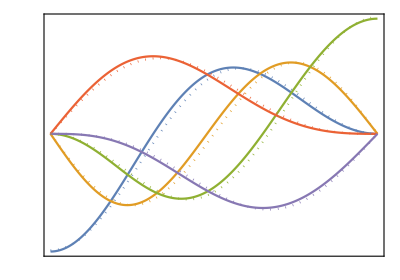
-Graphics--Graphics-

```mathematica
plot5={
ListPlot[swsh2/@list3,Joined->True],
Plot[SpinWeightedSphericalHarmonicY[-1,2,#,θ,0]&/@list3//Evaluate,{θ,0,π},PlotStyle->Dotted]
}//Labeled[Show[#,plotDirs,
PlotRangePadding->{0,0.02},
FrameLabel->{TeX@"\\theta",None},
FrameTicks->ticksSWSH2,
AspectRatio->0.7
],TeX["\\qquad{}_{-1}S_{2 m}(c=0.4 \\,; \\,\\theta, 0)"],Top,Spacings->{0,-0.6}]&
Export[thesisPath<>"plotSWSH2.pdf",plot5];
```

### Z Plot

```mathematica
ticksLogZ1={TicksParse@{"1","10^{-10}","10^{-20}","10^{-30}"},TicksParse@Range[0,1.2,0.2]};
```

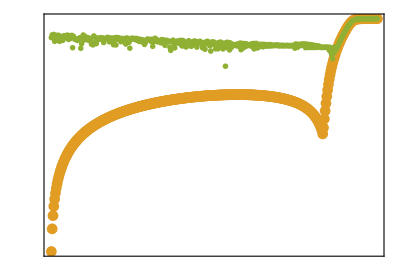
-Graphics--Graphics-

```mathematica
markers={▲,•,◼};
legend6={Style[#1,FontColor->ColorData[97,#2],FontSize->15]&@@@Transpose[{markers,Range[3]}],TeX[{"Z^{(1)}","Z^{(2)}","Z^{(3)}"}]}ᵀ//Grid//Panel;
plot6=ListLogPlot[Tuples[{{2#2/(3*#1)},Abs@{##3}}]&@@@ImportCSV[GetZFile[1,5,3,"singlePrecision"]]ᵀ,
Joined->{False,False,False},PlotMarkers->Evaluate@Tuples[{markers,{11}}],
plotDirs,
PlotRangePadding->{0,4},
FrameLabel->{TeX@"\\bar{\\omega}/ 3 \\bar{\\Omega}_H",None},
FrameTicks->ticksLogZ1,
AspectRatio->0.7
]//Legended[#,legend6]&//Labeled[#,TeX["|{}_{\\pm 1}Z_{5,3}|~(\\mathscr{J}=0.9999)\\hspace{1.5cm}"],Top,Spacings->{0,-0.6}]&
Export[thesisPath<>"noPrecisionZ53.pdf",plot6];
```

```mathematica
ticksLogZ1={TicksParse@{"1","10^{-5}","10^{-10}","10^{-15}","10^{-20}","10^{-25}","10^{-30}"},TicksParse@Range[0,1.2,0.2]};
```

```mathematica
list7={{1,1},{2,2},{3,3},{4,4},{5,5},{2,1},{3,2},{4,3},{5,4},{3,1},{4,2},{5,3}};
calloutPos7={
{0.64,Above},{0.75,Above},{0.84,Above},{0.86,Below},{0.94,Below},
{0.66,10^-5.5},{0.56,Below},{0.65,Below},{0.74,Below},
{0.84,Below},{0.92,Below},{0.98,After}
};
calloutAPos7={Automatic,Automatic,Automatic,Automatic,Automatic,
0.54,Automatic,Automatic,Automatic,
Automatic,Automatic,0.90
};
styleDirs7=Join[
Directive[Thickness[0.00335],ColorData[97,#]]&/@Range[1,5],
Directive[Thickness[0.00335],Dashed,ColorData[97,#]]&/@Range[2,5],
Directive[Thickness[0.00335],Dashing[{0.005,0.005}],ColorData[97,#]]&/@Range[3,5]
];
plot7=LogPlot[Table[
Callout[
Abs[Interpolation[Apply[{(2#2)/lm⟦2⟧,#3}&,ImportCSV[GetZFile[1,lm⟦1⟧,lm⟦2⟧,"singlePrecision"]]⟦All,{1,2,3}⟧,{1}]][x]],
TeXS[If[lm⟦1⟧==lm⟦2⟧==1,"\\ell, m = ",""]<>ToString@lm⟦1⟧<>", "<>ToString@lm⟦2⟧],lm[[3]],lm[[4]]],
{lm,Join[list7ᵀ,{calloutPos7},{calloutAPos7}]ᵀ}]//Evaluate,
{x,0.012,0.996},
ImageSize->Large,
Evaluate@plotDirs,
PlotStyle->styleDirs7,
PlotRangePadding->{0.01,{2,5}},
PlotRange->{{0,1.0},All},
FrameLabel->{TeX@"\\bar{\\omega}/ m \\bar{\\Omega}_H",None},
FrameTicks->ticksLogZ1,AspectRatio->1.3
]//Labeled[#,TeX["\\qquad{}_{\\pm 1}Z_{\\ell m}~(\\mathscr{J}=0.9999)"],Top,Spacings->{0,-0.6}]&
Export[thesisPath<>"precisionLogZ.pdf",plot7];
```

-Graphics--Graphics-

```mathematica
ticksZ2={TicksParse@Range[0,-1.0,-0.2],TicksParse@Range[0,1.2,0.2]};
```

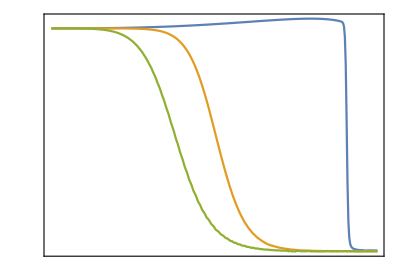
-Graphics--Graphics-

```mathematica
plot8=ListPlot[{2#2/#1,#3}&@@@ImportCSV[GetZFile[1,1,#1,"singlePrecision"]]⟦1;;-30⟧&/@list2,
plotDirs,Joined->True,
AspectRatio->0.7,
PlotRangePadding->{0,0.08},
FrameTicks->ticksZ2,
FrameLabel->{TeX@"\\bar{\\omega}/ \\bar{\\Omega}_H",None}
]//Labeled[#,TeX["\\qquad{}_{\\pm 1}Z_{1 m}~(\\mathscr{J}=0.9999)\\vspace{2cm}"],Top,Spacings->{0,-0.6}]&//
Legended[#,LineLegend[ColorData[97,#]&/@Range@Length@list2,TeX[list2],
LegendFunction->Panel,LegendLayout->"Column",LegendLabel->TeX["m"]]]&
Export[thesisPath<>"precisionZ1.pdf",plot8];
```

```mathematica
Z1=-4 ω̄ χ(2 ω̄)^(2l)(((l-s)!(l+s)!)/((2l)!(2l+1)!))^2 Product[(τ n)^2+4 χ^2,{n,1,l}];
```

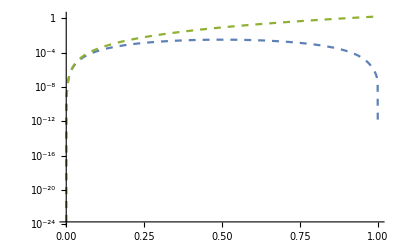

```mathematica
plot9=Chop@Expand[Z1//.{τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),s->1,m->#,𝒥->0.9999,l->1,ω̄->x Abs[m Ω̄]}]&/@{1,0,-1}//LogPlot[Abs@#//Evaluate,{x,0,1},PlotStyle->Dashed,PlotRange->All]&
```